## Уравнения

Someone told me that each equation I included in the book would halve the sales. 
Stephen Hawking
Мряка  и Бряка  расдрусили  пусик. Мряка  взяла  себе  два фарика, а Бряка - один. 
По сколько хрунечков у Мряки и у Бряки?
Григорий Остер. Ненаглядное пособие по математике

Solve : Finds a closed - form solution to single equations or systems
LinearSolve : Solves systems of linear equations when they are given in matrix form
FindRoot : Requires starting value (s) and uses numerical methods to find an approximatio to a single root
NSolve : Finds roots of polynomials
Reduce can reduce a system of equalities or inequalities to a simpler form, over reals or integers
FindInstance can find an instance of a system over reals or integers

### Solve

lhs == rhs

```mathematica
Solve[Sqrt[x^2+1]==x+2,x]
```

{{x→-3/4}}

```mathematica
Solve[a^3+3 a^2-3 a+1==0]
```

{{a→Root-3.85Root[1-3 #1+3 #1^2+#1^3&,1]-3.84732},{a→Root0.424-0.284 ⅈRoot[1-3 #1+3 #1^2+#1^3&,2]0.42366105093153633},{a→Root0.424+0.284 ⅈRoot[1-3 #1+3 #1^2+#1^3&,3]0.42366105093153633}}

```mathematica
Solve[a^3+3 a^2-3 a+1==0]//ToRadicals
```

{{a→-1-2^(1/3)-2^(2/3)},{a→-1+(1-ⅈ √3)/2^(1/3)+(1+ⅈ √3)/2^(2/3)},{a→-1+(1-ⅈ √3)/2^(2/3)+(1+ⅈ √3)/2^(1/3)}}

```mathematica
Solve[x^3+2 x^2-1==0,x]
```

{{x→-1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
Solve[x^6+2 x^5+2 x^3+3 x^2-4 x-4==0]
```

{{x→-2},{x→-1},{x→-1},{x→1},{x→1/2 (1-ⅈ √7)},{x→1/2 (1+ⅈ √7)}}

```mathematica
Solve[a x^2+b x+c==0]
```

{{c→-b x-a x^2}}

```mathematica
Solve[a x^2+b x+c==0,b]
```

{{b→(-c-a x^2)/x}}

{} 		
{{}}

```mathematica
Solve[{3 x+y==9,6 x +2 y==14}] (*нет решений*)
```

{}

```mathematica
Solve[x^2-1==(x+1)(x-1),x] (*справедливо для всех х*)
```

{{}}

```mathematica
Solve[{3 x+y==9,6 x +2 y==18}] (*справедливо для всех x таких, что ... *)
```

{{y→9-3 x}}

```mathematica
Solve[{3 x+y==9,6 x +2 y==18},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→9-3 x}}

Подстановки и замены

x -> y немедленная подстановка Rule[x, y]

```mathematica
Clear[x]
```

```mathematica
x^2+y/.{x->4} (*вместо x подствить 4*)
```

16+y

```mathematica
x^2+y/.{x->4,y->z}(*вместо x подствить 4, вместо y -> z*)
```

16+z

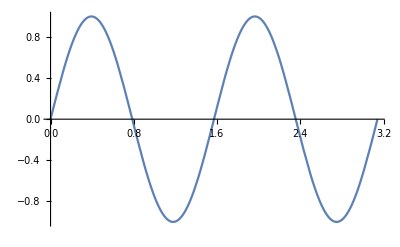

```mathematica
Plot[Sin[4 x],{x,0,π}]
```

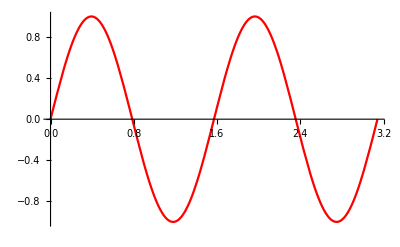

```mathematica
Plot[Sin[4 x],{x,0,π},PlotStyle->RGBColor[1,0,0]] (*заменить "стиль" кривой на "цвет красный"*)
```

```mathematica
s= Solve[x^6+2 x^5+2 x^3+3 x^2-4 x-4==0]
```

{{x→-2},{x→-1},{x→-1},{x→1},{x→1/2 (1-ⅈ √7)},{x→1/2 (1+ⅈ √7)}}

```mathematica
x/.s (*подстановка*)
```

{-2,-1,-1,1,1/2 (1-ⅈ √7),1/2 (1+ⅈ √7)}

```mathematica
x1=x/.s[[1]]
```

-2

```mathematica
y=x/.s[[2]]
```

-1

```mathematica
x=x/.s[[1]]
```

-2

```mathematica
Solve[x^6+2 x^5+2 x^3+3 x^2-4 x-4==0,x] (*ошибка, так как она помнит предыдущее х*)
```

Solve::ivar: -2 is not a valid variable.

Solve[True,-2]

1. Покажите, что x=(2c)/(∓√(b^2-4a c)-b) является решение уравнения  a x^2+b x+с=0 .

Вернемся к уравнениям

```mathematica
Clear[x,y]
```

```mathematica
Solve[x^7+x-1==0]
```

```mathematica
Solve[x^7+x-1==0]//ToRadicals
```

{{x→Root0.797Root[-1+#1+#1^7&,1].79654435412845714`},{x→Root-0.980-0.517 ⅈRoot[-1+#1+#1^7&,2]-0.9798083844899014},{x→Root-0.980+0.517 ⅈRoot[-1+#1+#1^7&,3]-0.9798083844899014},{x→Root-0.124-1.06 ⅈRoot[-1+#1+#1^7&,4]-0.12376188051147738},{x→Root-0.124+1.06 ⅈRoot[-1+#1+#1^7&,5]-0.12376188051147738},{x→Root0.705-0.638 ⅈRoot[-1+#1+#1^7&,6]0.7052980879371502},{x→Root0.705+0.638 ⅈRoot[-1+#1+#1^7&,7]0.7052980879371502}}

```mathematica
x/.N[%]
```

{0.796544,-0.979808-0.516677 ⅈ,-0.979808+0.516677 ⅈ,-0.123762-1.05665 ⅈ,-0.123762+1.05665 ⅈ,0.705298-0.637624 ⅈ,0.705298+0.637624 ⅈ}

```mathematica
(*Трансцендентные уравнения*)
```

```mathematica
Solve[3 Sin[x^2]==17]
```

{{x→ConditionalExpression[-√(π-ArcSin[17/3]+2 π C[1]), C[1]∈ℤ]},{x→ConditionalExpression[√(π-ArcSin[17/3]+2 π C[1]), C[1]∈ℤ]},{x→ConditionalExpression[-√(ArcSin[17/3]+2 π C[1]), C[1]∈ℤ]},{x→ConditionalExpression[√(ArcSin[17/3]+2 π C[1]), C[1]∈ℤ]}}

```mathematica
Solve[x Log[x]==2] (*решение в специальных функциях*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→2/ProductLog[2]}}

```mathematica
Reduce[x Log[x]==2]
```

x==ⅇ^ProductLog[2]

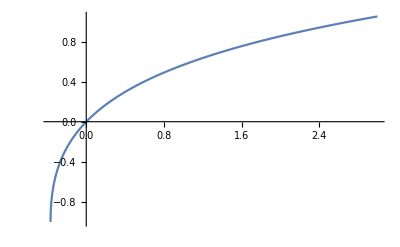

```mathematica
Plot[ProductLog[x],{x,-1/E,3}]
```

```mathematica
Series[ProductLog[z],{z,0,5}](*WM умееет работать со специальными функциями*)
```

z-z^2+(3 z^3)/2-(8 z^4)/3+(125 z^5)/24+O[z]^6

```mathematica
D[ProductLog[z],z]
```

ProductLog[z]/(z (1+ProductLog[z]))

Визуализация решения

```mathematica
Point[{x,0}/.sol]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Point[{x,0}/.sol]

```mathematica
sol=Solve[x^5-8 x^4+24 x^3-34 x^2+23 x-6==0,x]
```

{{x→1},{x→1},{x→1},{x→2},{x→3}}

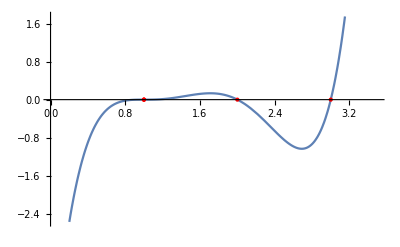

```mathematica
Plot[x^5-8 x^4+24 x^3-34 x^2+23 x-6,{x,0,3.5},Epilog->{PointSize[Large],Red,Point[{x,0}/.sol]}] (*Эпилог рисует то, что мы ему зададим. *)
```

Линейные уравнения и системы
Solve[eqns]
Solve[eqns,vars]

```mathematica
Clear[x,y]
```

```mathematica
sol=Solve[{x+2 y==7,2 x-y==4},{x,y}]
```

{{x→3,y→2}}

```mathematica
{x2,y2}={x,y}/.sol[[1]]
```

{3,2}

```mathematica
x3=x/.sol[[1,1]]
```

3

```mathematica
y3=y/.sol[[1,2]]
```

2

```mathematica
z=x/.sol[[1,2]] (*вернет х, потму что обращались к у*)
```

x

```mathematica
Clear[x,y]
```

```mathematica
sol1=Solve[{x+y==2 a,x-y==2 b},{x,y}]
```

{{x→a+b,y→a-b}}

```mathematica
{u,v}={x,y}/.sol1[[1]]
```

{a+b,a-b}

Solve[eqn,vars,elims]

```mathematica
Clear["Global`*"]
```

```mathematica
eqns={x-y==c,x+y==2 c};
Solve[eqns,{x,y}]
```

{{x→(3 c)/2,y→c/2}}

```mathematica
Solve[eqns,{x,y},{c}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→x/3}}

Графическое решение

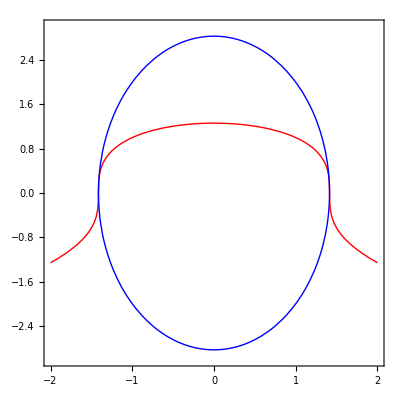

```mathematica
ContourPlot[{x^2+y^3-2==0,x^2+y^2/4-2==0},{x,-2,2},{y,-3,3},ContourStyle ->{{Red,Thick},{Blue,Thick}}] (*первое - поверхность, но функция показывает график в плоскости*)
```

```mathematica
Solve[{x^2+y^3-2==0,x^2+y^2/4-2==0},{x,y}] (*система уравнений*)
```

{{x→-√2,y→0},{x→√2,y→0},{x→-(√127)/8,y→1/4},{x→(√127)/8,y→1/4}}

```mathematica
pts = {x,y}/.Solve[{x^2+y^3-2==0,x^2+y^2/4-2==0},{x,y}](*корни*)
```

{{-√2,0},{√2,0},{-(√127)/8,1/4},{(√127)/8,1/4}}

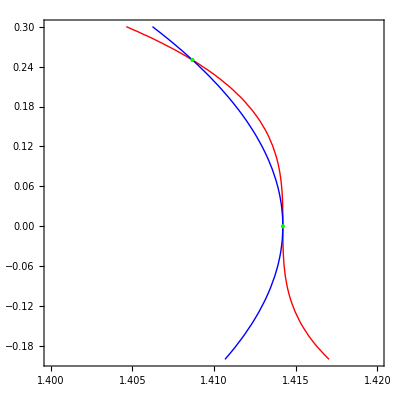

```mathematica
ContourPlot[{x^2+y^3-2==0,x^2+y^2/4-2==0},{x,1.4,1.42},{y,-0.2,0.3},ContourStyle ->{{Red,Thick},{Blue,Thick}},Epilog->{PointSize[Large],Green,Point[{pts⟦2⟧,pts[[4]]}]}]
```

2. Найти пары вещественных значений (x,y), удовлетворяющих уравнениям x^2 y+xy^2=2 и x^3 y+xy^3=3. Проиллюстрировать решение задачи.

3. Покажите графически, что x = y = 1 удовлетворяет уравнению   x^x+y^y=2 .

Немного о Reduce

```mathematica
Reduce[13 x^2< 10 && 5 x +2 >0] (*решили неравенство*)
```

-2/5<x<√(10/13)

```mathematica
sol=Reduce[x^3+13 x^2<10 && 5 x +2>0]
```

-2/5<x<Root0.850Root[-10+13 #1^2+#1^3&,3].84972695336142567`

```mathematica
sol⟦1⟧ (*⟦  --- Esc [[ Esc *)
```

-2/5

```mathematica
ToRadicals[sol⟦5⟧]
```

1/3 (-13+169/(-2062+3 ⅈ √63885)^(1/3)+(-2062+3 ⅈ √63885)^(1/3))

```mathematica
N[sol⟦5⟧] (*численно*)
```

0.849727

```mathematica
Reduce[Sin[x]==Cos[x],x](*общее решение тригонометрического уравнения*)
```

C[1]∈ℤ&&(x==-2 ArcTan[1+√2]+2 π C[1]||x==-2 ArcTan[1-√2]+2 π C[1])

```mathematica
s=Reduce[Sin[x]==Cos[x]+Tan[x],x,GeneratedParameters->(k &)] (*к - это параметр*)
```

k∈ℤ&&(x==2 k π+2 ArcTan[Root-4.44Root[1-2 #1^2+4 #1^3+#1^4&,1]-4.43911]||x==2 k π+2 ArcTan[Root-0.514Root[1-2 #1^2+4 #1^3+#1^4&,2]-.51361982956383123`]||x==2 k π+2 ArcTan[Root0.476-0.460 ⅈRoot[1-2 #1^2+4 #1^3+#1^4&,3]0.47636446820759276]||x==2 k π+2 ArcTan[Root0.476+0.460 ⅈRoot[1-2 #1^2+4 #1^3+#1^4&,4]0.47636446820759276])

```mathematica
2 ArcTan[Root[1-2 #1^2+4 #1^3+#1^4&,1]]//N
```

-2.69845

### LinearSolve

```mathematica
Clear["Global`*"];
```

```mathematica
A={{1,2,3},{4,5,6},{2,3,1}};b={1,2,1};
```

```mathematica
A.{x,y,z}
```

{x+2 y+3 z,4 x+5 y+6 z,2 x+3 y+z}

```mathematica
Solve[A.{x,y,z}==b]
```

{{x→-2/9,y→4/9,z→1/9}}

```mathematica
LinearSolve[A,b]
```

{-2/9,4/9,1/9}

```mathematica
LinearSolve[{{3,1},{6,2}},{9,4}](*нет решений*)
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{3,1},{6,2}},{9,4}]

```mathematica
Solve[{{3,1},{6,2}}.{x,y}=={9,4}]
```

{}

```mathematica
Det[{{3,1},{6,2}}]
```

0

```mathematica
LinearSolve[{{3,1},{6,2}},{9,18}] (*! одно из решений*)
```

```mathematica
{3,0}
```

{3,0}

```mathematica
Solve[{{3,1},{6,2}}.{x,y}=={9,18}](*!  семейство решений*)
```

{{y→9-3 x}}

```mathematica
a={{2,1,3},{1,1,1},{1,0,1}}
```

{{2,1,3},{1,1,1},{1,0,1}}

```mathematica
f=LinearSolve[a]
```

LinearSolveFunction[…]

```mathematica
b1={7,8,9};
b2={-4,5,6};
```

```mathematica
f[b1]
```

{19,-1,-10}

```mathematica
f[b2]
```

{21,-1,-15}

```mathematica
a.f[b1]
```

{7,8,9}

```mathematica
LinearSolve[a,{b1,b2}ᵀ]ᵀ (* aᵀ  - "a ESC tr ESC"*)
```

{{19,-1,-10},{21,-1,-15}}

RowReduce[a] Метод Гаусса

```mathematica
a//MatrixForm (*просто для иллюстрации, за матрицу не считает*)
```

(2 | 1 | 3
1 | 1 | 1
1 | 0 | 1)

```mathematica
b1//MatrixForm
```

(7
8
9)

```mathematica
m=Append[aᵀ,b1]ᵀ; m//MatrixForm
```

(2 | 1 | 3 | 7
1 | 1 | 1 | 8
1 | 0 | 1 | 9)

```mathematica
r=RowReduce[m];r//MatrixForm
```

(1 | 0 | 0 | 19
0 | 1 | 0 | -1
0 | 0 | 1 | -10)

```mathematica
r[[All,-1]]
```

{19,-1,-10}

Society for Industrial and Applied Mathematics (SIAM) contest

A={a_ij}: a_ii=i-ое простое число, a_ij=1, if |i-j|=2^k, a_ij=0 иначе
A^-1?

```mathematica
SparseArray[{{1,2}->5},5]
```

SparseArray[…]

```mathematica
Normal[%]
```

{{0,5,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
MatrixForm[%%]
```

(0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
n=5;
```

```mathematica
SparseArray[{{i_,i_}->Prime[i]},n]//MatrixForm (*Prime - простые числа*)
```

(2 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0
0 | 0 | 0 | 7 | 0
0 | 0 | 0 | 0 | 11)

```mathematica
Table[{i,i+2^j}->1,{i,n-1},{j,0,Log[2,n-i]}] (*дает список ненулевых*, выдается правило сразу)
```

{{{1,2}→1,{1,3}→1,{1,5}→1},{{2,3}→1,{2,4}→1},{{3,4}→1,{3,5}→1},{{4,5}→1}}

```mathematica
SparseArray[Flatten[Table[{i,i+2^j}->1,{i,n-1},{j,0,Log[2,n-i]}]],n]
(*Flatten - убирает список??*)
```

Table::iterb: Iterator {i, -1 + n} does not have appropriate bounds.

SparseArray::list: List expected at position 1 in SparseArray[Table[{i, i + 2^j} → 1, {i, -1 + n}, {j, 0, Log[2, n - i]}], n].

SparseArray[Table[{i,i+2^j}→1,{i,-1+n},{j,0,Log[2,n-i]}],n]

```mathematica
SparseArray[{{i_,i_}->Prime[i]},n]
```

SparseArray[…]

```mathematica
A=(SparseArray[{{i_,i_}->Prime[i]},n]+(#+Transpose[#])&)[SparseArray[Flatten[Table[{i,i+2^j}->1,{i,n-1},{j,0,Log[2,n-i]}]],n]] (*матрица + транспонированная*)
```

SparseArray[…]

```mathematica
MatrixForm[A]
```

(2 | 1 | 1 | 0 | 1
1 | 3 | 1 | 1 | 0
1 | 1 | 5 | 1 | 1
0 | 1 | 1 | 7 | 1
1 | 0 | 1 | 1 | 11)

```mathematica
Inverse[A]//MatrixForm (*обратная матрица*)
```

(982/1439 | -308/1439 | -133/1439 | 75/1439 | -84/1439
-308/1439 | 630/1439 | -55/1439 | -88/1439 | 41/1439
-133/1439 | -55/1439 | 336/1439 | -38/1439 | -15/1439
75/1439 | -88/1439 | -38/1439 | 227/1439 | -24/1439
-84/1439 | 41/1439 | -15/1439 | -24/1439 | 142/1439)

```mathematica
b=ConstantArray[0,n]; b⟦2⟧=1;
```

```mathematica
b
```

{0,1,0,0,0}

```mathematica
LinearSolve[A,b]
```

{-308/1439,630/1439,-55/1439,-88/1439,41/1439}

```mathematica
n=20000; b=ConstantArray[0,n]; b⟦1⟧=1;
```

```mathematica
A=(SparseArray[{{i_,i_}->Prime[i]},n]+(#+Transpose[#])&)[SparseArray[Flatten[Table[{i,i+2^j}->1,{i,n-1},{j,0,Log[2,n-i]}]],n]]
```

SparseArray[<554466>, {20000, 20000}]

```mathematica
LinearSolve[A,N[b],Method->{"Krylov",Method->"ConjugateGradient"}]⟦1⟧
```

0.725078

### NSolve

```mathematica
nsol = NSolve[x^11+x^7-3 x^2==0,x]
```

{{x→-1.01838+0.450107 ⅈ},{x→-1.01838-0.450107 ⅈ},{x→-0.645216-0.974665 ⅈ},{x→-0.645216+0.974665 ⅈ},{x→0.},{x→0.},{x→0.229107-1.04766 ⅈ},{x→0.229107+1.04766 ⅈ},{x→0.905162-0.797137 ⅈ},{x→0.905162+0.797137 ⅈ},{x→1.05865}}

```mathematica
(x^11+x^7-3 x^2==0)/.nsol (*равны только нулевые, неверно потому что численные решения*)
```

{False,False,False,False,True,True,False,False,False,False,False}

```mathematica
nsol2=NSolve[x^11+x^7-3 x^2==0,x,WorkingPrecision->10]
```

{{x→-1.018379727-0.450107116 ⅈ},{x→-1.018379727+0.450107116 ⅈ},{x→-0.645216398-0.9746647867 ⅈ},{x→-0.645216398+0.9746647867 ⅈ},{x→0},{x→0},{x→0.229107127-1.047658849 ⅈ},{x→0.229107127+1.047658849 ⅈ},{x→0.9051624744-0.797136662 ⅈ},{x→0.9051624744+0.797136662 ⅈ},{x→1.058653047}}

```mathematica
(x^11+x^7-3 x^2==0)/.nsol2 (*цитата: 10 цифр после запятой должны бть оправданы*)
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
nsol3=NSolve[{x^2+y^3-x y==0,x+y+x^2-1==0},{x,y}]
```

{{x→-2.06867,y→-1.21074},{x→-1.43152-0.695043 ⅈ,y→0.865346-1.2949 ⅈ},{x→-1.43152+0.695043 ⅈ,y→0.865346+1.2949 ⅈ},{x→0.397534+0.0995355 ⅈ,y→0.454339-0.178673 ⅈ},{x→0.397534-0.0995355 ⅈ,y→0.454339+0.178673 ⅈ},{x→1.13665,y→-1.42864}}

```mathematica
{x,y}/.nsol3
```

{{-2.06867,-1.21074},{-1.43152-0.695043 ⅈ,0.865346-1.2949 ⅈ},{-1.43152+0.695043 ⅈ,0.865346+1.2949 ⅈ},{0.397534+0.0995355 ⅈ,0.454339-0.178673 ⅈ},{0.397534-0.0995355 ⅈ,0.454339+0.178673 ⅈ},{1.13665,-1.42864}}

```mathematica
Element[2.4,Reals] (*проверка на принадлежность мн-ву действительных чисел*)
```

True

```mathematica
π∈Reals
```

True

```mathematica
Select[{x,y}/.nsol3,#[[1]]∈Reals&]
```

{{-2.06867,-1.21074},{1.13665,-1.42864}}

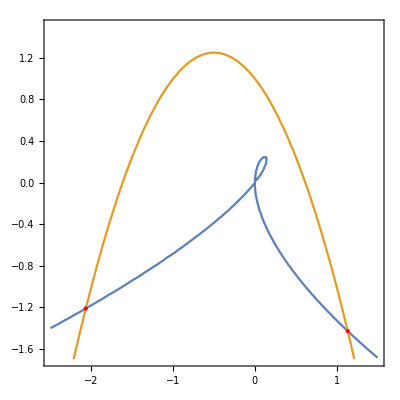

```mathematica
ContourPlot[{x^2+y^3-x y==0,x+y+x^2-1==0},{x,-2.5,1.5},{y,-1.7,1.5},Epilog->{PointSize[Large],Red,Point[Select[{x,y}/.nsol3,#[[1]]∈Reals&]]}]
```

### FindRoot

```mathematica
FindRoot[x^2-2==0,{x,1}] (*корень в окрестности единицы*)
```

{x→1.41421}

```mathematica
FindRoot[x^2-2==0,{x,1},AccuracyGoal -> 20,WorkingPrecision -> 30]
```

{x→1.41421356237309504880168872421}

```mathematica
FindRoot[Sin[x]==2,{x,1}] (*в вещественных числах нет, переход к комплексным*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→1.57079}

```mathematica
FindRoot[Sin[x]==2,{x,1+I}]
```

{x→1.5708+1.31696 ⅈ}

```mathematica
sol={x,y}/.FindRoot[{Sin[x y]==0.5,Cos[x+y^2]==0.6},{x,-1},{y,2.5}]
```

{-1.40916,2.60097}

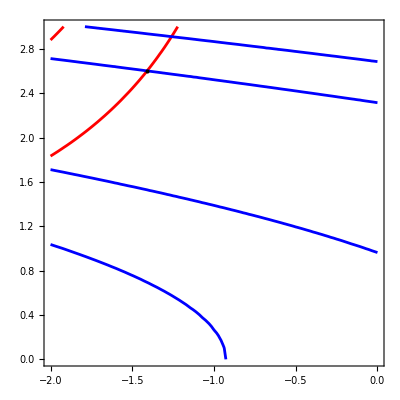

```mathematica
ContourPlot[{Sin[x y]==0.5,Cos[x+y^2]==0.6},{x,-2,0},{y,0,3},ContourStyle ->{{Red,Thickness[0.005]},{Blue,Thickness[0.005]}},Epilog->{PointSize[Large],Point[sol]}]
```

### Все корни на интервале

```mathematica
Clear[f]; f[x_]:=Sin[x^2]-ⅇ^(Cos[x]/2)+1; (*функция явная*)
```

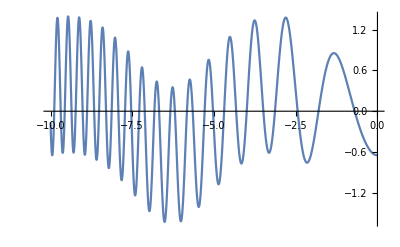

```mathematica
Plot[f[x],{x,-10,0}]
```

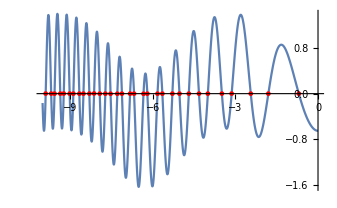

```mathematica
p=Plot[f[x],{x,-10,0},Mesh->{{0}},MeshFunctions->(f[#]&),MeshStyle->Directive[PointSize[0.01],Red]]
```

```mathematica
Normal[p]//FullForm
```

```mathematica
seeds=Cases[Normal[p],Point[z_]:>z⟦1⟧,Infinity] (*cases вытаскивает то, что уд-ет усл-ю*)
```

{-9.56594,-8.13027,-7.53136,-1.8029,-3.13515,-0.697188,-3.99885,-3.49028,-2.44128,-9.88729,-8.6654,-8.30176,-7.28654,-5.03017,-9.23154,-4.32148,-7.72152,-6.33532,-5.28739,-9.68787,-8.51613,-6.67897,-5.65119,-9.3574,-7.92447,-7.11866,-6.19685,-5.82711,-9.0169,-4.69063,-8.88232,-6.82341}

```mathematica
Table[x/.FindRoot[f[x],{x,s}],{s,seeds}]
```

Table::iterb: Iterator {s, seeds} does not have appropriate bounds.

Table[x/.FindRoot[f[x],{x,s}],{s,seeds}]

```mathematica
roots=Table[x/.FindRoot[f[x],{x,s}],{s,seeds}]∪(SameTest -> (Abs[#1-#2]<10^-6&))
```

{-9.88729,-9.68787,-9.56594,-9.3574,-9.23154,-9.0169,-8.88232,-8.6654,-8.51613,-8.30176,-8.13027,-7.92447,-7.72152,-7.53136,-7.28654,-7.11866,-6.82341,-6.67897,-6.33532,-6.19685,-5.82711,-5.65119,-5.28739,-5.03017,-4.69063,-4.32148,-3.99885,-3.49028,-3.13515,-2.44128,-1.8029,-0.697188}

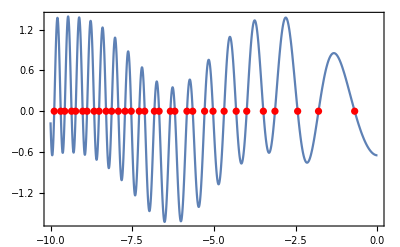

```mathematica
Plot[f[x],{x,-10,0},Epilog->{PointSize[0.013],Red,Point[Transpose[{roots,f[roots]}]]},Frame->True,Axes->False]
```

```mathematica
FindRoots[f_,{x_,a_,b_},opts___]:=Module[{p,seeds},p=Plot[f,{x,a-(b-a)/100,b+(b-a)/100},Mesh->{{0}},MeshFunctions->(f/.x->#1&),Evaluate[Sequence@@FilterRules[{opts},Options[Graphics]]]];
seeds=Union[Cases[Normal[p],Point[{z_,_}]:>z,Infinity],SameTest -> (Abs[#1-#2]<10^-6&)];
Select[If[seeds=={},{},Union[Table[Re[x]/.FindRoot[f==0,{x,s},Evaluate[Sequence@@FilterRules[{opts},Options[FindRoot]]]],{s,seeds}],(SameTest -> (Abs[#1-#2]<10^-6&))]],a≤#≤b&]]
```

```mathematica
g[x_]:=x/5 Cos[x]+Sin[x^3]
```

```mathematica
solns=FindRoots[g[x],{x,-3,3}]
```

{-2.95303,-2.77828,-2.6848,-2.48279,-2.34533,-2.09635,-1.85543,-1.46921,-8.60268×10^-23,1.46921,1.85543,2.09635,2.34533,2.48279,2.6848,2.77828,2.95303}

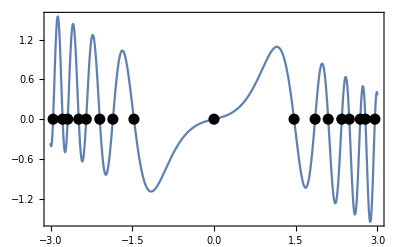

```mathematica
Plot[g[x],{x,-3,3},Frame->True,AxesStyle->GrayLevel[0.6],Epilog->{PointSize[0.02],Point[{#,0}&/@solns]}]
```

```mathematica
Reduce[g[x]==0&&-3<x<3,x]⟦1⟧
```

x==Root-2.95Root[{5 Sin[#1^3]+Cos[#1] #1&,-2.953032966665638812}]-2.95303

```mathematica
N[x/.{ToRules[Reduce[g[x]==0&&-3<x<3,x]]}]
```

{-2.95303,-2.77828,-2.6848,-2.48279,-2.34533,-2.09635,-1.85543,-1.46921,0.,1.46921,1.85543,2.09635,2.34533,2.48279,2.6848,2.77828,2.95303}

4. Найти корни функции f(x)=sin(x^2)-cos(x^3) в интервале 0 ≤ x ≤ π. Отобразить найденные решения на графике

5. Найти, при каких натуральных значениях x и y значение выражение  f(x,y)=2 xy^4+x^2 y^3-2 x^3 y^2-y^5-x^4 y+2 y является 10е число Фибоначи

6. Пусть A_n матрица  n х n с элементом (i, j) равным x^(|i-j-ij|+ij) . 
а) Найти все значения x, при которых дискриминант матрицы равен 0 для  n = 3, 4
б) Найти все различные x, для которых det(A_6)=0